## Change in soil quality and the cumulative soil quality for a set sequence

```mathematica
setseq={1,1,1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,-1,-1,-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,1,1,-1,-1,-1,1,1,1,1,1,-1,-1,-1,1,1,1,1,1,-1,-1,1,-1};
```

```mathematica
seq=setseq;
accsoil=Accumulate[seq];
```

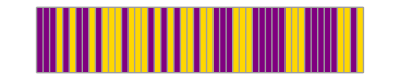

```mathematica
gold=RGBColor["#FFD700"];
ArrayPlot[{seq},ColorRules->{1->Purple,-1->gold},Mesh->True]
```

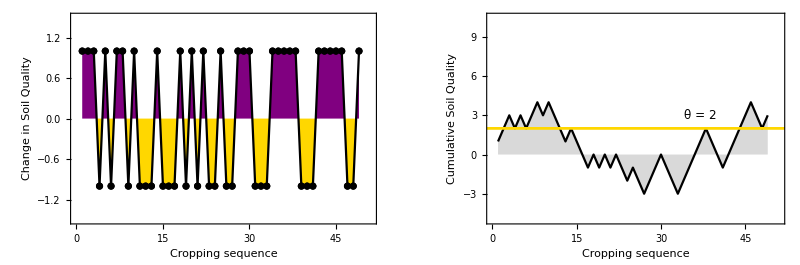

```mathematica
GraphicsRow[{ListPlot[seq⟦1;;Length[seq]-1⟧,PlotRange->{{0,51},{-1.5,1.5}},Frame->True,Joined->True,FrameStyle->{Black,Thickness[0.002]},AxesOrigin->{1,0},PlotStyle->Black,
FrameLabel->{Style["Cropping sequence",14,Black],Style["Change in Soil Quality",14,Black]},Mesh->Full,Filling->{1->{Axis,{gold,Purple}}}],
ListPlot[accsoil⟦1;;Length[seq]-1⟧,PlotRange->{{0,51},{-5,10.5}},PlotStyle->Black,Frame->True,Joined->True,FrameStyle->{Black,Thickness[0.002]},
FrameLabel->{Style["Cropping sequence",14,Black],Style["Cumulative Soil Quality",14,Black]},Filling->{1->{Axis,LightGray}},GridLines->{None,{2}},GridLinesStyle->Directive[gold,Thickness[0.005]],Method->{"GridLinesInFront"->True},Epilog->Inset[Style["θ = 2",12],{37,3}]]}]
```

## Simulating trajectories for cumulative profit

```mathematica
numberofsimulations=1000;

p=0.2;
p1=0.5;
p2=0.9;
profit=seq/.{1->-1,-1->1};
createtrajectories[maxruns_]:=Module[{max=maxruns},
runs={};
For[numerofruns=1,numerofruns≤max,numerofruns++,
trajectory={};
For[i=1,i≤Length[profit],i++,
If[profit⟦i⟧==-1,AppendTo[trajectory,If[RandomReal[]<p,1,-1]]];
If[profit⟦i⟧==1,AppendTo[trajectory,If[accsoil⟦i⟧>2,If[RandomReal[]<p2,1,-1],If[RandomReal[]<p1,1,-1]]]];
];
AppendTo[runs,Accumulate[trajectory]]
]
]
```

```mathematica
createtrajectories[numberofsimulations]
```

```mathematica
won=0;
If[#>0,won++]&/@runs⟦All,Length[seq]⟧;
```

```mathematica
colorscheme=If[#>0,Red,Directive[GrayLevel[0.9],Opacity[0.5]]]&/@runs⟦All,50⟧;
profits=ListPlot[runs,Joined->True,PlotStyle->colorscheme,Frame->True,FrameStyle->{Black,Thickness[0.002]},
FrameLabel->{Style["Cropping sequence",14,Black],Style["Profits",14,Black]}];
pie=PieChart[{won/numberofsimulations//N,1-won/numberofsimulations//N},ChartLegends->{"Profit making trajectories","Trajectories incurring loss"}];
```

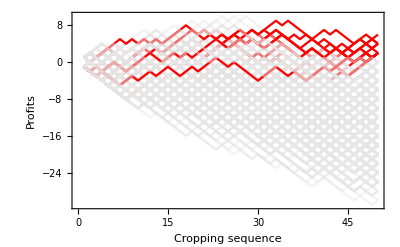

```mathematica
GraphicsRow[{profits,pie},ImageSize->Full]
```